```mathematica
D[2 ArcTan[Exp[t-a]Tan[ya/2]],t]
```

(2 ⅇ^(-a+t) Tan[ya/2])/(1+ⅇ^(-2 a+2 t) Tan[ya/2]^2)

```mathematica
Sin[2 ArcTan[Exp[t-a]Tan[ya/2]]]
```

Sin[2 ArcTan[ⅇ^(-a+t) Tan[ya/2]]]

```mathematica
DSolve[{y'[t]==Sin[y[t]],y[a]==ya},y[t],t]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{y[t]→2 ArcCot[ⅇ^(a-t) Cot[ya/2]]}}

```mathematica
D[2 ArcCot[ⅇ^(a-t) Cot[ya/2]],t]
```

(2 ⅇ^(a-t) Cot[ya/2])/(1+ⅇ^(2 a-2 t) Cot[ya/2]^2)

```mathematica
Sin[2 ArcCot[ⅇ^(a-t) Cot[ya/2]]]
```

Sin[2 ArcCot[ⅇ^(a-t) Cot[ya/2]]]

```mathematica
7/4+(19/8)/4
```

75/32

```mathematica
5/8+(5/8-7/4)/4
```

11/32

```mathematica
75/32+(75/32+11/32)/4
```

193/64

```mathematica
11/32+(11/32-75/32)/4
```

-5/32

```mathematica
s=DSolve[{y1'[t]==y1[t]+y2[t],y2'[t]==-y1[t]+y2[t],y1[0]==1,y2[0]==0},{y1[t],y2[t]},t]
```

{{y1[t]→ⅇ^t Cos[t],y2[t]→-ⅇ^t Sin[t]}}

```mathematica
N[E]Cos[1]
-N[E]Sin[1]
```

1.46869

-2.28736

```mathematica
N[119/64]
N[15/8]
```

1.85938

1.875

```mathematica
5/4+(5/4-1/4)/4
```

3/2

```mathematica
-1/4+(-5/4-1/4)/4
```

-5/8

```mathematica
3/2+(3/2-5/8)/4
```

55/32

```mathematica
-5/8-(3/2+5/8)/4
```

-37/32

```mathematica
55/32+(55/32-37/32)/4
```

119/64

```mathematica
-37/32-(55/32+37/32)/4
```

-15/8

```mathematica
5/4+(5/4-5/16+5/4+(5/4-5/16)/4-5/16+(-5/4-5/16)/4)/8
```

375/256

```mathematica
N[375/256]
```

1.46484

```mathematica
-5/16+(-5/4-5/16-5/4-(5/4-5/16)/4-5/16+(-5/4-5/16)/4)/8
```

-25/32

```mathematica
N[-25/32]
```

-0.78125

```mathematica
375/256+(375/256-25/32+(375/256+(375/256-25/32)/4)+(-25/32+(-375/256-25/32)/4))/8
```

1625/1024

```mathematica
N[1625/1024]
```

1.58691

```mathematica
-25/32+(-375/256-25/32-(375/256+(375/256-25/32)/4)+(-25/32+(-375/256-25/32)/4))/8
```

-5875/4096

```mathematica
N[-5875/4096]
```

-1.43433

```mathematica
1625/1024+(1625/1024-5875/4096+(1625/1024+(1625/1024-5875/4096)/4)+(-5875/4096+(-1625/1024-5875/4096)/4))/8
```

100625/65536

```mathematica
N[100625/65536]
```

1.53542

```mathematica
-5875/4096+(-1625/1024-5875/4096-(1625/1024+(1625/1024-5875/4096)/4)+(-5875/4096+(-1625/1024-5875/4096)/4))/8
```

-9375/4096

```mathematica
N[-9375/4096]
```

-2.28882

```mathematica
Clear[y]
DSolve[{y'[t]==5t^4y[t],y[0]==1},y[t],t]
```

{{y[t]→ⅇ^(t^5)}}

```mathematica
1+1/4 5 (1/8)^4(1+1/8 5 0^4 1)
```

16389/16384

```mathematica
16389/16384+1/4 5 (1/4+1/8)^4 (16389/16384+1/8 5 (1/4)^4 16389/16384)
```

563550465933/549755813888

```mathematica
563550465933/549755813888+1/4 5 (1/2+1/8)^4 (563550465933/549755813888+1/8 5 (1/2)^4 563550465933/549755813888)
```

1416076649135725941/1152921504606846976

```mathematica
1416076649135725941/1152921504606846976+1/4 5 (3/4+1/8)^4 (1416076649135725941/1152921504606846976+1/8 5 (3/4)^4 1416076649135725941/1152921504606846976)
```

89216648054273453335862877/38685626227668133590597632

```mathematica
N[89216648054273453335862877/38685626227668133590597632]
```

2.3062

```mathematica
N[E]
```

2.71828

```mathematica
DSolve[{y'[t]==t^2y[t],y[0]==1},y[t],t]
```

{{y[t]→ⅇ^(t^3/3)}}

```mathematica
s=NDSolve[{y''[t]==y[t]^2,y[1]==1/3,y[2]==1/12},{y[t],y'[t]},t]
```

{{y[t]→InterpolatingFunction[…][t],y'[t]→InterpolatingFunction[…][t]}}

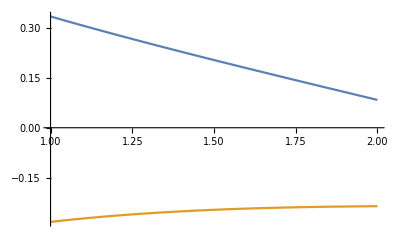

```mathematica
Plot[{y[t]/.s,y'[t]/.s},{t,1,2}]
```